```mathematica
dataQ = {{0,N[64*π]},{0.01/4, 201.064370710888},{0.02/4,201.0668117637175},{0.03/4,201.069253148827},{0.04/4,201.07169500657213 },{0.05/4,201.07413745039446},{0.07/4,201.07902439823897},{0.1/4,201.08636035993376}}
```

{{0,201.062},{0.0025,201.064},{0.005,201.067},{0.0075,201.069},{0.01,201.072},{0.0125,201.074},{0.0175,201.079},{0.025,201.086}}

```mathematica
Dimensions[dataQ][[1]]
```

8

```mathematica
dataDeltaQ = Table[{dataQ [[i]][[1]],dataQ [[i]][[2]] - dataQ [[1]][[2]]},{i,1,Dimensions[dataQ][[1]]}]
```

{{0,0.},{0.0025,0.00244088},{0.005,0.00488193},{0.0075,0.00732332},{0.01,0.00976518},{0.0125,0.0122076},{0.0175,0.0170946},{0.025,0.0244305}}

```mathematica
Fit[dataDeltaQ,{x},x]
```

0.976943 x

```mathematica
0.9769427415273068/4
```

0.244236

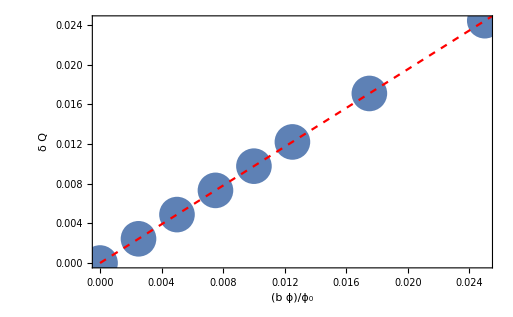

```mathematica
Show[ListPlot[dataDeltaQ,PlotStyle->PointSize[0.05]],Plot[0.9769427415273068x,{x,0,0.1},PlotStyle->{Dashed,Red}],Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{ b ϕ/Subscript[ϕ, 0],δ Q}]
```